```mathematica
Physics 128L Nonlinear Model Fit examples
```

```mathematica
(*First I will invent some data.  Ignore this step for your real lab data!  My made-up data will be the sum of several components: a constant ... *) 
fakedata = Table[3.45 ,{i,1,30}];
(* ... and a Gaussian peak centered around 19... *) 
fakedata = Table[fakedata[[i]] + 5.67*E^-((i-18.78)/.978)^2,{i,1,30}];
(* ... and, what the heck, some Gaussian random noise. I'll make the noise worse on the right, that's the sort of thing that might happen.*)
fakedata = Table[fakedata[[i]] +RandomReal[NormalDistribution[0,0.1+i*i/500]],{i,1,30}];
myErrors =Table[0.1+i*i/500,{i,1,30}]
```

{0.102,0.108,0.118,0.132,0.15,0.172,0.198,0.228,0.262,0.3,0.342,0.388,0.438,0.492,0.55,0.612,0.678,0.748,0.822,0.9,0.982,1.068,1.158,1.252,1.35,1.452,1.558,1.668,1.782,1.9}

{{1,3.37328},{2,3.36266},{3,3.405},{4,3.22577},{5,3.5101},{6,3.23278},{7,3.22169},{8,3.31234},{9,3.2686},{10,3.90014},{11,3.21861},{12,3.28047},{13,2.46522},{14,3.90975},{15,3.72547},{16,3.14163},{17,3.8529},{18,6.66366},{19,9.79932},{20,4.68811},{21,4.26994},{22,3.54733},{23,1.98806},{24,2.28225},{25,3.73309},{26,5.14791},{27,2.04268},{28,2.52839},{29,3.32793},{30,3.67088}}

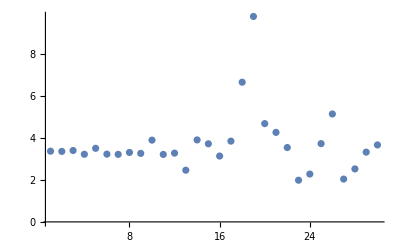

{{{1,3.37328},ErrorBar[0.102]},{{2,3.36266},ErrorBar[0.108]},{{3,3.405},ErrorBar[0.118]},{{4,3.22577},ErrorBar[0.132]},{{5,3.5101},ErrorBar[0.15]},{{6,3.23278},ErrorBar[0.172]},{{7,3.22169},ErrorBar[0.198]},{{8,3.31234},ErrorBar[0.228]},{{9,3.2686},ErrorBar[0.262]},{{10,3.90014},ErrorBar[0.3]},{{11,3.21861},ErrorBar[0.342]},{{12,3.28047},ErrorBar[0.388]},{{13,2.46522},ErrorBar[0.438]},{{14,3.90975},ErrorBar[0.492]},{{15,3.72547},ErrorBar[0.55]},{{16,3.14163},ErrorBar[0.612]},{{17,3.8529},ErrorBar[0.678]},{{18,6.66366},ErrorBar[0.748]},{{19,9.79932},ErrorBar[0.822]},{{20,4.68811},ErrorBar[0.9]},{{21,4.26994},ErrorBar[0.982]},{{22,3.54733},ErrorBar[1.068]},{{23,1.98806},ErrorBar[1.158]},{{24,2.28225},ErrorBar[1.252]},{{25,3.73309},ErrorBar[1.35]},{{26,5.14791},ErrorBar[1.452]},{{27,2.04268},ErrorBar[1.558]},{{28,2.52839},ErrorBar[1.668]},{{29,3.32793},ErrorBar[1.782]},{{30,3.67088},ErrorBar[1.9]}}

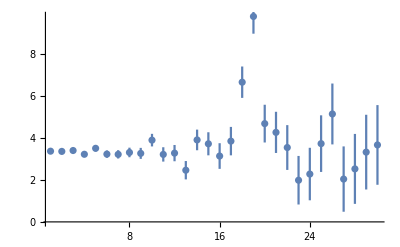

```mathematica
(* and I'll build that into a ListPlot-style table. *) 
datalist = Table[{i,fakedata[[i]]},{i,1,30}]
ListPlot[datalist,PlotRange->All]
(* I'll toss in the error-bar version too. *)
Needs["ErrorBarPlots`"]
datalistwitherrors = Table[{{i,fakedata[[i]]},ErrorBar[myErrors[[i]]]},{i,1,30}]
myListPlot = ErrorListPlot[datalistwitherrors,PlotRange->All]
```

-Graphics-

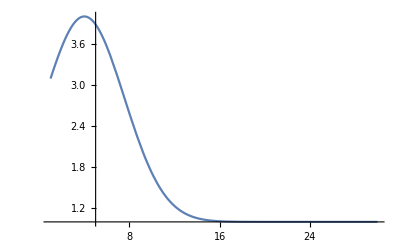

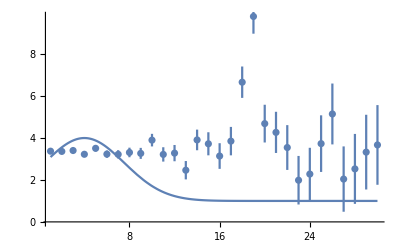

```mathematica
(* OK, I generally expect this data to look like the following function: *)
dumbidea = Plot[a +  b*E^(-((x-c)/d)^2), {x,1,30}]
(* but that's not plottable.  You can't plot variables, and in the above equation a,b,c,d, are just variables.   You can only plot them if everything is numeric. *)
guessedLinePlot = Plot[1.0 +  3.0*E^(-((x-4.0)/5.0)^2),{x,1,30}]
(* that's obviously not QUITE the right function, because the "true" values of the parameters are not 1,2,3,4,5.  Therefore, this attempt at the function did NOT give me a function that describes where the data is:*)
Show[myListPlot,guessedLinePlot] 
(* In principle, one thing you could do is KEEP GUESSING.   Improve your guesses---for example, make the Gaussian narrower and move its center to the right---until you find agreement.   That's a perfectly fine thing to do, but tedious. *)
```

3.87208-0.680812 ⅇ^(-0.04 (-4.+x)^2)

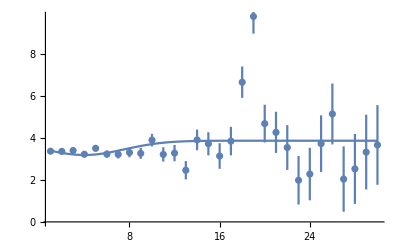

```mathematica
(* "Fit" functions are built to automate the trial-and-error process of trying-and-retrying these functions.    The simple function "Fit" or |"FindFit" is easy to use, but it only works with  *multipliers.*   It can't find parameters that go into exponents, or trig functions, or whatever.  You give it a list of terms, it figures how to add them together.*) 
myDumbFit= Fit[datalist,{1, E^(-((x-4.0)/5.0)^2)},x]
Show[myListPlot,Plot[myDumbFit,{x,1,30}]]
(* Notice that it made a pretty good guess at the constant-offset, but it had no way to manipulate the width or position of the bump.  In this case it actually gave us a negative bump.*)
```

FittedModel[3.97701-0.805047 ⅇ^(-0.0255229 «1»)]

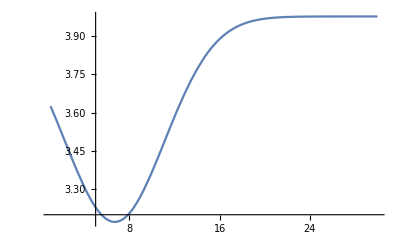

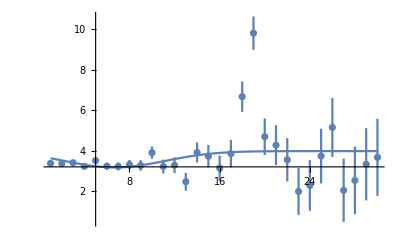

| Estimate | Standard Error | t-Statistic | P-Value
a | 3.97701 | 0.432189 | 9.20202 | 1.16326×10^-9
b | -0.805047 | 0.766763 | -1.04993 | 0.303412
c | 6.6969 | 4.68828 | 1.42843 | 0.165071
d | -6.25943 | 8.41044 | -0.744246 | 0.463402

```mathematica
(* To do anything else we need a NONLINEAR fit, with the power to manipulate any parameter anywhere.  *)
myNLM = NonlinearModelFit[datalist,a +  b*E^(-((x-c)/d)^2),{a,b,c,d},x]
myNLMPlot = Plot[myNLM[x],{x,1,30},PlotRange->All]

Show[myNLMPlot,myListPlot]
myNLM["ParameterTable"]
(* amazing!  It worked.   Sometimes it doesn't work --- a common problem is that the automated "guesswork" process has to start somewhere, and improve gradually.  (The default is to start ALL of the parameters at 1.000.)   If the first few guesses aren't going in the right direction, it gives up ... sometimes by failing, sometimes by finding a god-awful fit (this is called "getting stuck in a local minimum") Always plot your results to make sure your fit is reasonable*)
```

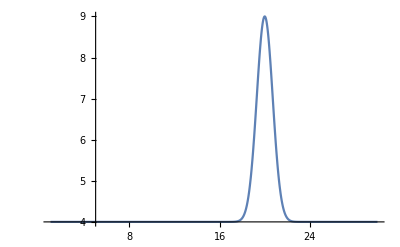

FittedModel[3.31584+6.70078 ⅇ^(-1.04466 «1»)]

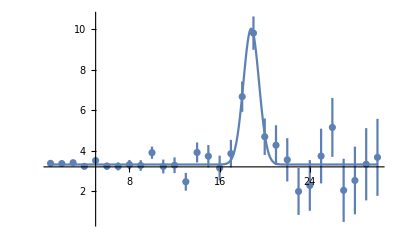

| Estimate | Standard Error | t-Statistic | P-Value
a | 3.31584 | 0.129232 | 25.658 | 5.42325×10^-20
b | 6.70078 | 0.72331 | 9.26406 | 1.01605×10^-9
c | 18.8023 | 0.0930103 | 202.153 | 4.303×10^-43
d | 0.97839 | 0.122009 | 8.01899 | 1.69195×10^-8

```mathematica
(* the NonlinearModelFit will almost always work IF you have a good guess at the parameters.   Tell the fitter to start with a reasonable ballpark guess, and it'll do all of the optimization smoothly.   In this case, I can provide some OK guesses by just eyeballing the function.*)

Plot[4 +  5*E^(-((x-20)/1)^2),{x,1,30},PlotRange->All]
myNLMGood = NonlinearModelFit[datalist,a +  b*E^(-((x-c)/d)^2),{{a,4},{b,5},{c,20},{d,1}},x]
Show[Plot[myNLMGood[x],{x,1,30},PlotRange->All],myListPlot]
myNLMGood["ParameterTable"]
(* Perfect!  Notice that the fitter has gotten "the right answers" in this case---it has found values consistent (i.e. within about an error bar) with the "truth" that was responsible for generating this data in the first place.*)
```

{9.80392,9.25926,8.47458,7.57576,6.66667,5.81395,5.05051,4.38596,3.81679,3.33333,2.92398,2.57732,2.28311,2.03252,1.81818,1.63399,1.47493,1.3369,1.21655,1.11111,1.01833,0.93633,0.863558,0.798722,0.740741,0.688705,0.641849,0.59952,0.561167,0.526316}

FittedModel[3.34431+6.67671 ⅇ^(-1.05511 «1»)]

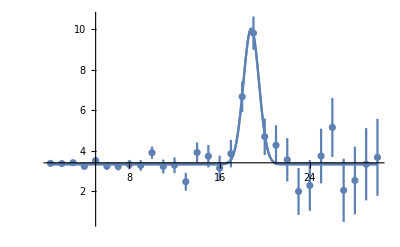

{ | Estimate | Standard Error | t-Statistic | P-Value
a | 3.34431 | 0.0726221 | 46.0509 | 1.88108×10^-26
b | 6.67671 | 0.662541 | 10.0774 | 1.8051×10^-10
c | 18.8017 | 0.0857944 | 219.149 | 5.28164×10^-44
d | 0.973534 | 0.113191 | 8.60078 | 4.43133×10^-9, | Estimate | Standard Error | t-Statistic | P-Value
a | 3.31584 | 0.129232 | 25.658 | 5.42325×10^-20
b | 6.70078 | 0.72331 | 9.26406 | 1.01605×10^-9
c | 18.8023 | 0.0930103 | 202.153 | 4.303×10^-43
d | 0.97839 | 0.122009 | 8.01899 | 1.69195×10^-8}

```mathematica
(* The next question is about error bars.   What do you do if your data points have errors on them?   How do you tell NonLinearFit about the error bars?   (Notice that I did not feed the error-bar data into the fit, just the points.)  It turns out that what you need to do is to *weight* the points.  A point with a large error bar E is downweighted by 1/El, so the fitter relies on it less heavily.   A point with a small error bar Es should be weighted heavily, as 1/Es.  Let's turn our list of errors into a list of weights.*)
(*I'll start with the errors that I invented for this problem.  In reality, you should use your actual errors*)

myWeights = 1/myErrors
myNLMWeighted = NonlinearModelFit[datalist,a +  b*E^(-((x-c)/d)^2),{{a,4},{b,5},{c,20},{d,1}},x,Weights->myWeights]

(* I'll compare the data and the old and new fits. *)
Show[Plot[myNLMWeighted[x],{x,1,30},PlotRange->All],Plot[myNLMGood[x],{x,1,30},PlotRange->All],myListPlot]
{myNLMWeighted["ParameterTable"],myNLMGood["ParameterTable"]}
```